#### params

```mathematica
Δ=0.005;
σ=0.01;
α=0.001;
ϕ=0.001;
γ=10;
κ=50;
ε=0.005;
Υ=Δ+ε;
χ=0.02;
tiltλ=50/300;
λ=tiltλ*ⅇ^(-κ*Δ);


Ν=10;(*Total Amt*)
T=300;(*Total Time*)
```

```mathematica
(*Market Impact Cost*)
c[q_]:=α*q;
```

```mathematica
(*Target Schedule*)
IS[t_]:=Ν*(1-Sinh[χ*(T-t)]/Sinh[χ*T])
```

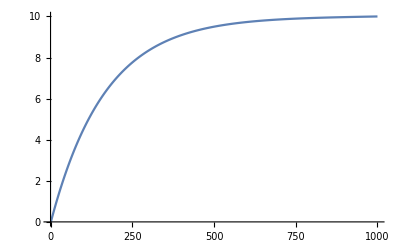

```mathematica
ListLinePlot[Table[IS[i],{i,Reverse@time}]]
```

#### eqs

```mathematica
ω[t_,q_]:=ⅇ^(-κ*(Υ+c[Ν-q])*(Ν-q))/;t==T
ω[t_,q_]:=Exp[-κ*ϕ*NIntegrate[(Ν-IS[u])^2,{u,t,T}]]/;q==Ν
```

尝试解析解 建议告辞

```mathematica
eqs=(D[ω[t,q],t]-κ*ϕ*(q-IS[t])^2 ω[t,q]+ⅇ^-1 λ ω[t,q+1])*(ω[t,q]-ⅇ^(-κ*Υ)ω[t,q+1])==0
```

(ω[t,q]-0.606531 ω[t,1+q]) (-0.05 (q-10 (1-0.00495753 Sinh[0.02 (300-t)]))^2 ω[t,q]+0.122626 ω[t,1+q]+ω^(1,0)[t,q])==0

数值解尝试
Do it backwards

```mathematica
time=Reverse@N@Subdivide[0,T,1000-1];(*Time*)
inventory=Reverse@Range[Ν]; (*Quantity Domain*)
Tω=Table[ω[T,q],{q,inventory}]; (*Terminal Time Vals*)
Qω=Table[ω[t,Ν],{t,time}];(*Terminal Quantity Vals*)
```

```mathematica
time[[1]]
```

300.

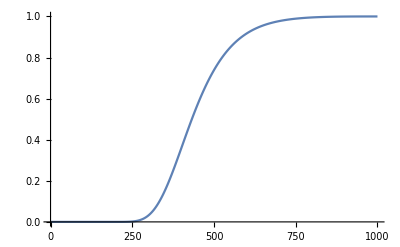

```mathematica
ListLinePlot[Reverse@Qω]
```

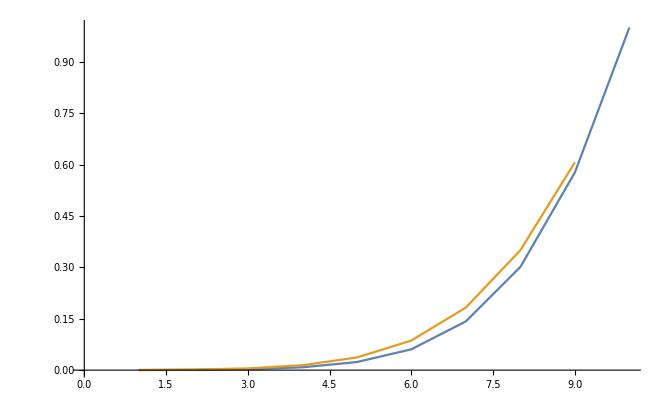

```mathematica
ListLinePlot[{Reverse[Tω],ⅇ^(-κ*Υ)*Reverse[Tω][[2;;]]}]
```

```mathematica
ω[T,1]
```

0.000193545

```mathematica
ω[T,2]*ⅇ^(-κ*Υ)
```

0.000452827

```mathematica
ω[T,Ν]
```

1.

```mathematica
Table[ω[T,q]≥ⅇ^(-κ*Υ)*ω[T,q+1],{q,0,9}]
```

{False,False,False,False,False,False,False,False,False,False}

```mathematica
Table[ω[T,q]≥ ⅇ^(-κ*Υ)*ω[T,q+1],{q,1,Ν-1}]
```

{False,False,False,False,False,False,False,False,False}

```mathematica
Table[ω[T,q],{q,1,Ν}]
```

{0.000193545,0.000746586,0.00260584,0.00822975,0.0235177,0.0608101,0.142274,0.301194,0.57695,1.}

```mathematica
Table[ω[T,q+1],{q,1,Ν-1}]
```

{0.000746586,0.00260584,0.00822975,0.0235177,0.0608101,0.142274,0.301194,0.57695,1.}

```mathematica
timeStep=Abs@First@Differences@time
```

0.3003

```mathematica
fdmSolve[timeInitial_,qInitial_,stepSize_,inventory_,time_]:=Module[
{Qforward=timeInitial,
Tforward=qInitial,
lastVal=0},
Table[
Module[
{row=0},
row=If[idxQ==1,
Tforward,
(*Given a Q level, iterate through time*)
Table[
Module[{
curTime=time[[idxT]],
curQ=inventory[[idxQ]],
prvTimeVal=0,
prvQVal=Tforward[[idxT]],
checkCons,
temp1=0,
temp2=0,
cur=0
},
temp1=If[curTime==T,ω[T,curQ],(ⅇ*prvTimeVal+timeStep*λ*prvQVal)/(ⅇ(1+ϕ*timeStep*κ*(curQ-IS[curTime])^2))];
temp2=If[curTime==T,ω[T,curQ],prvQVal*ⅇ^(-κ*Υ)];(*MO trigger*)
checkCons[curVal_]:=(prvTimeVal-curVal)/timeStep-κ*ϕ*(curQ-IS[curTime])^2*curVal+ⅇ^-1*λ*prvQVal≤0&&curVal≥ ⅇ^(-κ*Υ)*prvQVal;
cur=If[checkCons[temp1],temp1,temp2];
prvTimeVal=cur;
If[checkCons[cur],PrependTo[bool,{inventory[[idxQ]],time[[idxT]]}]];
cur
],
{idxT,1, Length[time]}]
];
Tforward=row;
row],
{idxQ,1,Length@inventory}]]
```

```mathematica
τ={};
bool={};
m=fdmSolve[Tω,Qω,timeStep,inventory,time];
```

```mathematica
Tω
```

{1.,0.57695,0.301194,0.142274,0.0608101,0.0235177,0.00822975,0.00260584,0.000746586,0.000193545}

```mathematica
ⅇ^(-κ*Υ)≤ Tω[[2]]
```

False

```mathematica
Length@bool
```

7425

```mathematica
bool
```

{{1,12.9129},{1,13.2132},{1,13.5135},{1,13.8138},{1,14.1141},{1,14.4144},{1,14.7147},{1,15.015},{1,15.3153},{1,15.6156},{1,15.9159},7404,{9,71.4715},{9,71.7718},{9,72.0721},{9,72.3724},{9,72.6727},{9,72.973},{9,73.2733},{9,73.5736},{9,73.8739},{9,74.1742}}
 |  |  |  |

```mathematica
τ
```

{1,1,1,1,1,1,1,1,1}

```mathematica
ListPlot[IS[time[[τ]]]]
```

-Graphics-

```mathematica
Qforward= Tω;(*prv time val*)
Tforward=Qω;(*prv Q val*)
lastVal=0;

mat1=Table[(*Iterate through Q*)

Module[{row=0},
row=If[idxQ==1,
Tforward,
(*Given a Q level, iterate through time*)
Table[
Module[{
curTime=time[[idxT]],
curQ=inventory[[idxQ]],
prvTimeVal=0,
prvQVal=Tforward[[idxT]],
checkCons,
temp1=0,
temp2=0,
cur=0
},
temp1=If[curTime==T,Tω[[idxQ]],(ⅇ*prvTimeVal+timeStep*λ*prvQVal)/(ⅇ(1+ϕ*timeStep*κ*(curQ-IS[curTime])^2))];
temp2=If[curTime==T,Tω[[idxQ]],prvQVal*ⅇ^(-κ*Υ)];
checkCons[curVal_]:=(prvTimeVal-curVal)/timeStep-κ*ϕ*(curQ-IS[curTime])^2*curVal+ⅇ^-1*λ*prvQVal≤0&&curVal≥ ⅇ^(-κ*Υ)*prvQVal;
cur=If[checkCons[temp1],temp1,temp2];
(*cur=If[checkCons[temp1],temp1,-1];*)
prvTimeVal=cur;
cur],
{idxT,1, Length[time]}]
];
Tforward=row;
row]
,{idxQ,1,Length[inventory]}];



Qforward= Tω;(*prv time val*)
Tforward=Qω;(*prv Q val*)
lastVal=0;
mat2=Table[(*Iterate through Q*)

Module[{row=0},
row=If[idxQ==1,
Tforward,
(*Given a Q level, iterate through time*)
Table[
Module[{
curTime=time[[idxT]],
curQ=inventory[[idxQ]],
prvTimeVal=0,
prvQVal=Tforward[[idxT]],
checkCons,
temp1=0,
temp2=0,
cur=0
},
temp1=If[curTime==T,Tω[[idxQ]],(ⅇ*prvTimeVal+timeStep*λ*prvQVal)/(ⅇ(1+ϕ*timeStep*κ*(curQ-IS[curTime])^2))];
(*temp2=If[curTime==T,Tω[[idxQ]],prvQVal*ⅇ^(-κ*Υ)];
checkCons[curVal_]:=(prvTimeVal-curVal)/timeStep-κ*ϕ*(curQ-IS[curTime])^2*curVal+ⅇ^-1*λ*prvQVal≤0&&curVal≥ ⅇ^(-κ*Υ)*prvQVal;
cur=If[checkCons[temp2],temp2,temp1];*)
(*cur=If[checkCons[temp1],temp1,-1];*)
cur=temp1;
prvTimeVal=cur;
cur],
{idxT,1, Length[time]}]
];
Tforward=row;
row]
,{idxQ,1,Length[inventory]}];
(*(*Given a Q level, iterate through time*)
Length@Table[
Module[{
curTime=time[[idxT]],
curQ=inventory[[idxQ]],
prvTimeVal=0,
prvQVal=Tforward[[idxT]],
temp=0
},
temp=If[curTime==T,Tω[[idxQ]],(prvTimeVal+ⅇ^-1*λ*prvQVal)/(1+timeStep*κ*(curQ-IS[curTime])^2)];
prvTimeVal=temp;
temp],
{idxT,1, Length[time]}]*)
```

```mathematica
Thread[mat1==mat2]
```

False

```mathematica
hDiff=With[{m=Transpose[1/κ*Log[mat1]]},
-Differences[m,1]]
```

{{3.28024×10^-13,-0.00234568,-0.00716049,-0.0144444,-0.0241975,-0.0364198,-0.0511111,-0.0682716,-0.0879012,-0.11},2997,{0.00998335,0.00998335,0.00998335,4,0.00998335,0.00998335,0.00998335}}
 |  |  |  |

```mathematica
Map[Thread[#== Υ]&,hDiff]
```

{{False,False,False,False,False,False,False,False,False,False},{False,False,False,False,False,False,False,False,False,False},{False,False,False,False,False,False,False,False,False,False},2993,{False,False,False,False,False,False,False,False,False,False},{False,False,False,False,False,False,False,False,False,False},{False,False,False,False,False,False,False,False,False,False}}
 |  |  |  |

```mathematica
AnyTrue[hDiff,TrueQ[#>Υ]&,2]
```

False

```mathematica
1/κ*Log[mat2]
```

{{0.,-3.28024×10^-13,-2.62419×10^-12,-8.85669×10^-12,-2.09938×10^-11,-4.10037×10^-11,-7.08551×10^-11,-1.12516×10^-10,2984,-2.43061,-2.44036,-2.45014,-2.45997,-2.46983,-2.47974,-2.48968,-2.49966},8,{1}}
 |  |  |  |

```mathematica
ωval = Reverse[Reverse[mat2,2]];
```

```mathematica
toShow =Flatten[Table[{Reverse[time][[i]],Reverse[inventory][[j]],ωval[[j]][[i]]},{i,1,Length[time]},{j,1,Length[inventory]}],1];
```

```mathematica
ListPlot3D@toShow
```

-Graphics3D-

```mathematica
With[{m=Map[1/κ*Log[#]&,mat2]},m[[-2]]-m[[-1]]]
```

```mathematica
hval=Map[1/κ*Log[#]&,ωval];
```

```mathematica
Transpose[hval]
```

{{-2.58966,-2.57966,-2.56966,-2.55966,-2.54966,-2.53966,-2.52966,-2.51966,-2.50966,-2.49966},{-2.57968,-2.56968,-2.55968,-2.54968,-2.53968,-2.52968,-2.51968,-2.50968,-2.49968,-2.48968},2997,{-0.2,-0.167901,-0.138272,-0.111111,-0.0864198,-0.0641975,-0.0444444,-0.0271605,-0.0123457,0.}}
 |  |  |  |

```mathematica
Map[Differences,Transpose[hval]]
```

{{0.10184,0.101963,0.102328,0.102922,0.103725,0.104711,0.105855,0.107127,0.108501},{0.10184,0.101959,0.10232,0.102909,0.103708,0.104692,0.105833,0.107103,0.108475},{0.10184,0.101955,0.102311,0.102897,0.103692,0.104673,0.105811,0.107079,0.10845},2994,{0.109952,0.108501,0.107127,0.105855,0.104711,0.103724,0.102922,0.102328,0.101963},{0.109952,0.108501,0.107127,0.105855,0.104711,0.103725,0.102922,0.102328,0.101963},{0.0320988,0.0296296,0.0271605,0.0246914,0.0222222,0.0197531,0.017284,0.0148148,0.0123457}}
 |  |  |  |

```mathematica
Reverse[1/κ* Log[Tω]]
```

{-0.2,-0.167901,-0.138272,-0.111111,-0.0864198,-0.0641975,-0.0444444,-0.0271605,-0.0123457,0.}

```mathematica
hval[[-1]][[;;3]]
```

{-2.49966,-2.48968,-2.47974}

```mathematica
hval[[-2]][[;;3]]
```

{-2.50966,-2.49968,-2.48974}

```mathematica
δval=1/κ-Differences[hval];(*The optimal depth of limit order*)
```

```mathematica
δval
```

#### Price Dynamics

```mathematica
S0=100
```

100

```mathematica
𝒫=TransformedProcess[S0+σ*(up[t]-down[t]),{up\[Distributed]PoissonProcess[γ],down\[Distributed]PoissonProcess[γ]},t];
```

```mathematica
data = RandomFunction[𝒫,{0,T,1},10]
```

TemporalData[…]

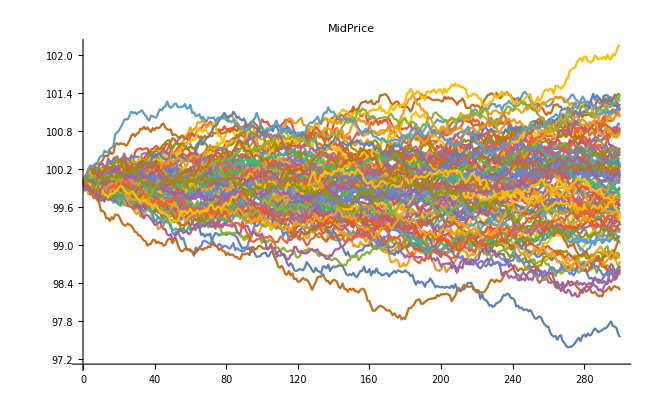

```mathematica
ListLinePlot[ RandomFunction[𝒫,{0,T,1},100],PlotLabel->"MidPrice"]
```